```mathematica
PP[n_, k_] := Sum[ 1/k - PP[n/j, k+1], { j, 2, n }]
```

```mathematica
PP[105,1]
```

458/15

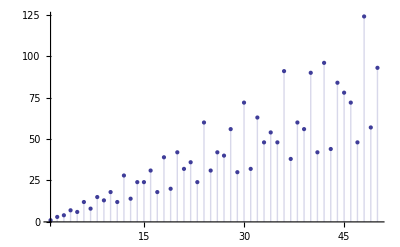

```mathematica
DiscretePlot[DivisorSum[n,#&],{n,50}]
```

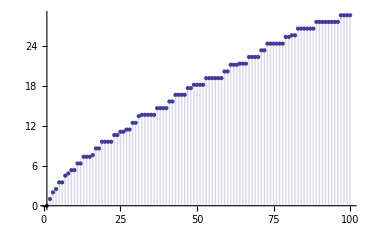

```mathematica
DiscretePlot[PP[n,1],{n,100}]
```

```mathematica
PS[n_] := FullSimplify[MangoldtLambda[ n]/Log[n]]
```

```mathematica
PS[25]
```

1/2

```mathematica
QQ[n_, k_, a_] := Sum[ PS[j](a^k/k! + QQ[n/j, k+1,a]), {j,2,n}]
```

```mathematica
QQ[100,1,1]
```

99

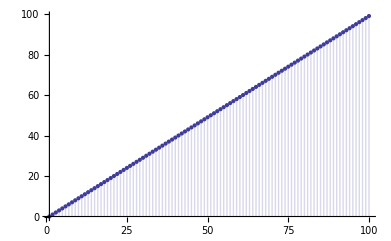

```mathematica
DiscretePlot[QQ[n,1,1],{n,100}]
```

```mathematica
QR[n_, a_] := N[QQ[n,1,a]/a]
```

```mathematica
QR[100,.00001]
```

28.5338

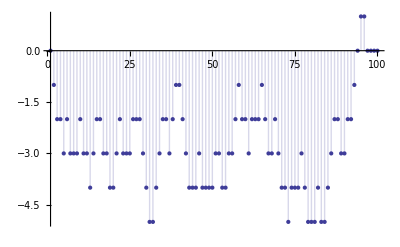

```mathematica
DiscretePlot[-QR[n,-1],{n,100}]
```

```mathematica
MM[n_]:=Sum[ MoebiusMu[ j ], {j,2,n}]
```

```mathematica
DiscretePlot[MM[n],{n,100}]
```

-Graphics-

```mathematica
DivisorSum[ 6, #&]
```

12

```mathematica
DD[ n_, 2]:=DivisorSum[n,Function[m,1]]
```

```mathematica
DD[12,2]
```

```mathematica
DD[ n_, k_ ] := DivisorSum[ n, Function[ m, DD[ n/m, k-1]]]
```

```mathematica
DD[6,4]
```

16

```mathematica
DDD[ n_, k_ ]:=Sum[ DD[j,k], {j,1,n}]
```

```mathematica
DDD[100,2]
```

482

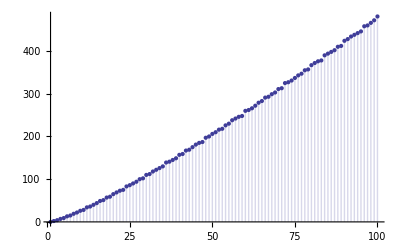

```mathematica
DiscretePlot[QR[n,2]*2,{n,100}]
```

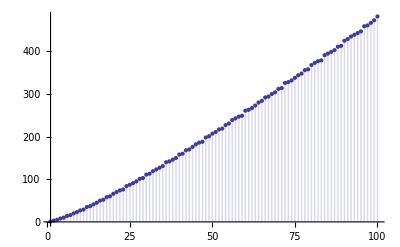

```mathematica
DiscretePlot[DDD[n,2],{n,100}]
```

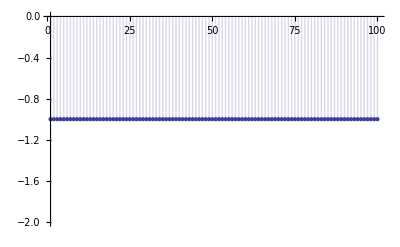

```mathematica
DiscretePlot[QR[n,2]*2 - DDD[n,2],{n,100}]
```

```mathematica
DiscretePlot[QR[n,3]*3 - DDD[n,3],{n,100}]
```

-Graphics-

```mathematica
DiscretePlot[QR[n,4]*4 - DDD[n,4],{n,100}]
```

-Graphics-

```mathematica
PPP[n_, k_, a_] := Sum[a MoebiusMu[j]( 1/k - PPP[n/j, k+1,a]), { j, 2, n }]
PPQ[n_, a_] := PPP[n,1,a]/a
```

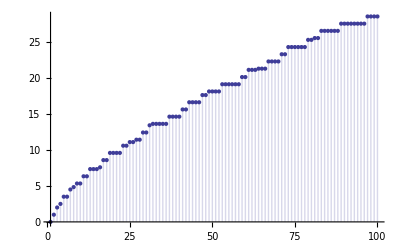

```mathematica
DiscretePlot[-PPQ[n,1],{n,100}]
```

```mathematica
PPR[n_, k_, a_] := Sum[a ( 1/k - PPR[n/j, k+1,a]), { j, 2, n }]
PPS[n_, a_] := PPR[n,1,a]/a
```

```mathematica
DiscretePlot[PPS[n,1],{n,100}]
```

-Graphics-

```mathematica
PPT[n_, k_] :=  (Floor[n] - n) - Sum[PPT[n/j, k+1], { j, 2, n }]
```

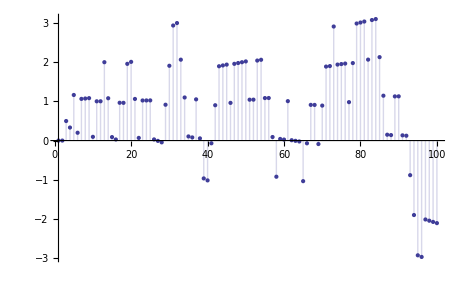

```mathematica
DiscretePlot[PPT[n,.000001],{n,100}]
```

```mathematica
Binomial[3,1]
```

3

```mathematica
PPD[n_, k_] := Sum[ DD[j,4](1/k - PPD[n/j, k+1]), { j, 2, n }]
```

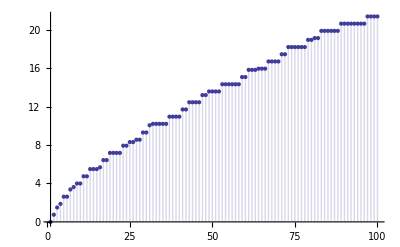

```mathematica
DiscretePlot[PPD[n,1]/4,{n,100}]
```

```mathematica
QS[n_, a_] := N[(QQ[n,1,a] - QQ[n-1,1,a])/a]
```

```mathematica
QS[99,1]
```

1.

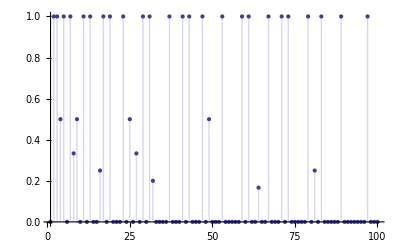

```mathematica
DiscretePlot[QS[n,0.00000001],{n,100}]
```

```mathematica
PPE[n_, k_] := Sum[ QS[j,1](1/k - PPE[n/j, k+1]), { j, 2, n }]
```

```mathematica
DiscretePlot[PPE[n,1]/1,{n,100}]
```

-Graphics-

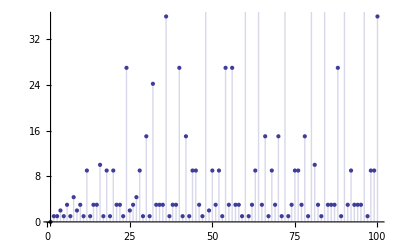

```mathematica
DiscretePlot[PPS[n,-2]-PPS[n-1,-2],{n,100}]
```

```mathematica
PSA[n_, a_ ] := PPS[n,a]-PPS[n-1,a]
```

```mathematica
PSA[26,2]
```

-1

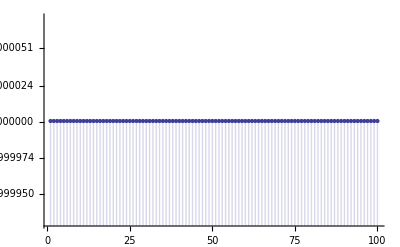

```mathematica
DiscretePlot[Re[PSA[53,(-.001 + 2 *(n/100))]] ,{n,100}]
```

```mathematica
PSA[23,4]
```

1

```mathematica
PPR[n_, k_, a_] := Sum[a ( 1/k - PPR[n/j, k+1,a]), { j, 2, n }]
PPS[n_, a_] := PPR[n,1,a]/a
```

```mathematica
DiscretePlot[Re[PPS[46,1+I(-221.001 + 422 *(n/100))]] ,{n,100}]
```

```mathematica
Table[PDF[BinomialDistribution[50,p],k],{p,{0.3,0.5,0.8}}]
DiscretePlot[Evaluate[%],{k,1,50}]
```

{Piecewise[{{0.3^k 0.7^(50-k) Binomial[50,k], 0≤k≤50}, {0, True}}],Piecewise[{{8.88178×10^-16 Binomial[50,k], 0≤k≤50}, {0, True}}],Piecewise[{{0.2^(50-k) 0.8^k Binomial[50,k], 0≤k≤50}, {0, True}}]}

```mathematica
DiscretePlot3D[PDF[MultivariatePoissonDistribution[3,{1,1}],{t,u}],{t,0,10},{u,0,10}]
```

```mathematica
DiscretePlot3D[PPS[i, 1+j*.05+.000001],{j,-30,30},{i,102,200},ExtentSize->Full]
```

```mathematica
DiscretePlot3D[PPS[i, 1+j*.05+.000001],{j,-30,30},{i,2,30},ExtentSize->Full]
```

-Graphics3D-